```mathematica
x[t_]:= -2 +2UnitStep[t+2]-Ramp[t+2]+Ramp[t+1]+Ramp[t]-2Ramp[t-2];
```

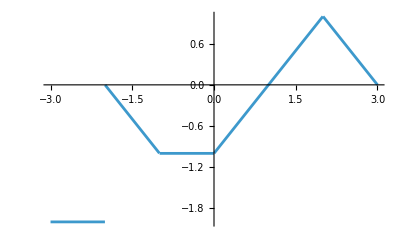

```mathematica
Plot[{x[t]},{t,-3,3}]
```

```mathematica
y[t_]=-1+UnitStep[t+2]+Ramp[t+2]-Ramp[t]-4UnitStep[t-1]+2Ramp[t-1]-2Ramp[t-2]
```

-1-2 Ramp[-2+t]+2 Ramp[-1+t]-Ramp[t]+Ramp[2+t]-4 UnitStep[-1+t]+UnitStep[2+t]

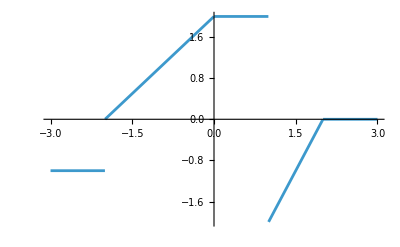

```mathematica
Plot[{y[t]},{t,-3,3}]
```

```mathematica
z1[t_]:=(x[2t]+y[t+1])UnitBox[t/4];
```

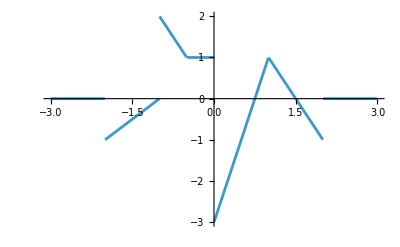

```mathematica
Plot[{z1[t]},{t,-3,3}]
```

```mathematica
z2[t_]:=y[2t-1]DiracDelta[t^2+3t-4];
```

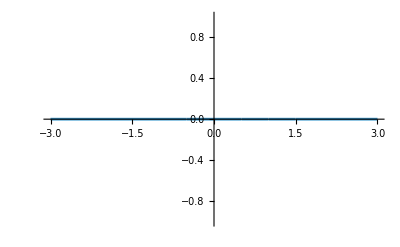

```mathematica
Plot[{z2[t]},{t,-3,3}]
```